# Alkali atom magnetic field shifts and branching ratios

The math presented here relies heavily on https://steck.us/alkalidata/cesiumnumbers.1.6.pdf

#### Declare constants

```mathematica
ℏ = 1; 
h = 2*Pi*ℏ; 
μB = 1.399624604; 
(* Cesium 133 values *)

gI = -0.00039885395; 
gJGs = 2.00254032; 
gJEs = 1.334; 
totIGs = 7/2; 
totIEs = 7/2; 
totJGs = 1/2; 
totJEs = 3/2; 
AhfsGs=2.2981579425  10^3; (* in MHz *)
BhfsGs=0;
ChfsGs=0;
AhfsEs=50.28827; (* in MHz *)
BhfsEs=-0.4934 ; (* in MHz *)
ChfsEs=0.560 10^-3;(* in MHz *)

(* End Cs 133 values *)

(* Li 6 values *)

(*gI = 0.0004476540; 
gJGs = 2.0023010; 
gJEs = 1.335; 
totIGs = 1; 
totIEs = 1; 
totJGs = 1/2; 
totJEs = 3/2; 
AhfsGs=152.1368407; (* in MHz *)
BhfsGs=0;
ChfsGs=0;
AhfsEs=-1.155; (* in MHz *)
BhfsEs=-0.10 ; (* in MHz *)
ChfsEs=0;(* in MHz *)*)

(*End Li 6 values *)
```

#### Solve ground state

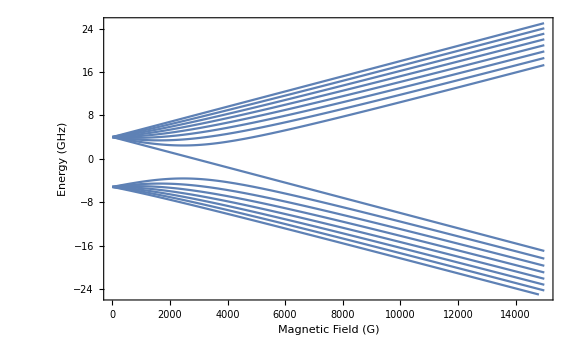

```mathematica
nStatesGs=(2totIGs+1)*(2totJGs+1);
IzGs=DiagonalMatrix[Table[mi,{mi,-totIGs,totIGs}]];
JzGs=DiagonalMatrix[Table[mj,{mj,-totJGs,totJGs}]];
IplusGs=DiagonalMatrix[Table[√(totIGs(totIGs+1)-mi(mi+1)),{mi,-totIGs,totIGs-1}],-1];
IminusGs=Transpose[IplusGs];
JplusGs=DiagonalMatrix[Table[√(totJGs(totJGs+1)-mj(mj+1)),{mj,-totJGs,totJGs-1}],-1];
JminusGs=Transpose[JplusGs];
JxGs=1/2(JplusGs+JminusGs);
JyGs=1/(2I)(JplusGs-JminusGs);
IxGs=1/2(IplusGs+IminusGs);
IyGs=1/(2I)(IplusGs-IminusGs);
JidGs=IdentityMatrix[2totJGs+1];
IidGs=IdentityMatrix[2totIGs+1];
OpOuter[a_,b_]:=Flatten[Outer[Times,a,b],{{1,3},{2,4}}];
IzGs=OpOuter[JidGs,IzGs];
JzGs=OpOuter[JzGs,IidGs];
IxGs=OpOuter[JidGs,IxGs];
JxGs=OpOuter[JxGs,IidGs];
IyGs=OpOuter[JidGs,IyGs];
JyGs=OpOuter[JyGs,IidGs];
HhfsSimpleGs=AhfsGs(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs);
HhfsHigherOrderGs=If[Abs[BhfsGs]>0,BhfsGs((3(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^2+3/2(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)-totIGs(totIGs+1)totJGs(totJGs+1))/(2totIGs(2totIGs-1)totJGs(2totJGs-1)))+ChfsGs(10(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^3+20(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^2+2(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)(totIGs(totIGs+1)+totJGs(totJGs+1)+3-3totIGs(totIGs+1)totJGs(totJGs+1))-5totIGs(totIGs+1)totJGs(totJGs+1))/(totIGs(totIGs-1)(2totIGs-1)totJGs(totJGs-1)(2totJGs-1)),0];
HzeemanGs=μB(gJGsJzGs+gIIzGs)Bz;
{evalsGs,evecsGs}=Eigensystem[HzeemanGs+HhfsSimpleGs];
evecsGs=Simplify[Table[evecsGs[[ii]]/Sqrt[Total[Conjugate[evecsGs[[ii]]].evecsGs[[ii]]]],{ii,1,nStatesGs}],Bz∈Reals];
energiesGs=Simplify[Table[Conjugate[evecsGs[[ii]]].(HzeemanGs+HhfsSimpleGs+HhfsHigherOrderGs).evecsGs[[ii]],{ii,1,nStatesGs}],Bz∈Reals];
mIlistGs=Table[IzGs[[ii,ii]],{ii,1,nStatesGs}];mJlistGs=Table[JzGs[[ii,ii]],{ii,1,nStatesGs}];FlistGs=Flatten[Table[Table[F,{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]];mFlistGs=Flatten[Table[Table[mF,{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]];mImJtoFmFGs=Quiet[Transpose[Table[Flatten[Table[Table[ClebschGordan[{totIGs,mIlistGs[[ii]]},{totJGs,mJlistGs[[ii]]},{F,mF}],{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]],{ii,1,nStatesGs}]]];evecsHighFieldGs=Chop[N[evecsGs/.Bz->10^10],10^-4];
evecsLowFieldGs=Chop[N[evecsGs/.Bz->0],10^-4];
IJcomponentsGs[vec_]:=Module[{max,indmax},
	indmax=Ordering[Abs[vec],-1][[1]];
	{mIlistGs[[indmax]], mJlistGs[[indmax]]}
];
FmFcomponentsGs[vec_]:=Module[{max,indmax,FmFvec},
	FmFvec=mImJtoFmFGs.vec;indmax=Ordering[Abs[FmFvec],-1][[1]];{FlistGs[[indmax]],mFlistGs[[indmax]]}];
{mIhighfieldGs,mJhighfieldGs}=Transpose[Table[IJcomponentsGs[evecsHighFieldGs[[ii]]],{ii,1,nStatesGs}]];
{FlowfieldGs,mFlowfieldGs}=Transpose[Table[FmFcomponentsGs[evecsLowFieldGs[[ii]]],{ii,1,nStatesGs}]];
evecsFmFGs=Table[mImJtoFmFGs.evecsGs[[ii]],{ii,1,nStatesGs}];
Plot[energiesGs*10^-3,{Bz,0,15000},ImageSize->Large,Frame->True,FrameLabel->{"Magnetic Field (G)","Energy (GHz)"},PlotRange->{{0,15000},{-25,25}}]
(*Plot[energiesGs*10^-3,{Bz,0,1000},ImageSize->Large,Frame->True,FrameLabel->{"Magnetic Field (G)","Energy (GHz)"},PlotRange->{{0,1000},{-2,2}}]*)
```

```mathematica
Differences[Sort[energiesGs/.Bz->880]]
Differences[Sort[energiesGs/.Bz->895]]
(*NumberForm[Sort[energiesGs/.Bz->895][[16]]-Sort[energiesGs/.Bz->895][[1]],9]*)
```

{260.493,273.866,289.545,308.276,331.203,360.173,7124.1,397.444,359.19,330.22,307.293,288.562,272.884,259.51,247.926}

{264.168,277.894,294.018,313.329,337.042,367.137,7090.74,406.123,366.137,336.043,312.33,293.018,276.895,263.169,251.299}

```mathematica
Sort[D[energiesGs,Bz]/.Bz->890]
```

{-1.39945,1.39945,-2.60008+1.42187 Conjugate'[0.283396],-2.22642+1.29299 Conjugate'[0.409182],-1.7619+0.941911 Conjugate'[0.454862],-1.81581+1.15067 Conjugate'[0.51277],-1.35826+0.991108 Conjugate'[0.60748],-1.11375+0.757145 Conjugate'[0.610242],-0.839143+0.808712 Conjugate'[0.699246],-0.565418+0.596966 Conjugate'[0.714881],-0.23586+0.5947 Conjugate'[0.792215],-0.0877139+0.454865 Conjugate'[0.794335],0.337407+0.32662 Conjugate'[0.858526],0.489047+0.334294 Conjugate'[0.890562],0.721852+0.209346 Conjugate'[0.912453],1.07388+0.10098 Conjugate'[0.959003]}

```mathematica
N[energiesGs[[1]]/.Bz->895,9]
```

2769.27

```mathematica
NumberForm[2769.2700000368295,16]
```

2769.27000003683

#### Solve excited state

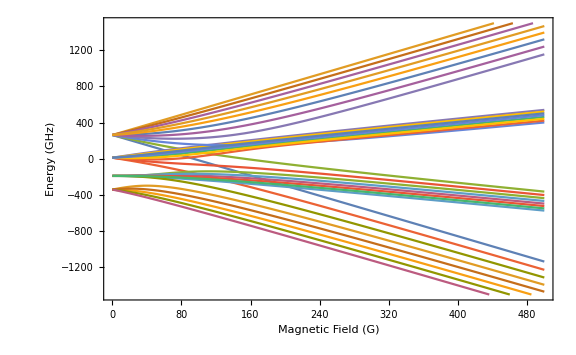

```mathematica
nStatesEs=(2totIEs+1)*(2totJEs+1);
IzEs=DiagonalMatrix[Table[mi,{mi,-totIEs,totIEs}]];
JzEs=DiagonalMatrix[Table[mj,{mj,-totJEs,totJEs}]];
IplusEs=DiagonalMatrix[Table[√(totIEs(totIEs+1)-mi(mi+1)),{mi,-totIEs,totIEs-1}],-1];
IminusEs=Transpose[IplusEs];
JplusEs=DiagonalMatrix[Table[√(totJEs(totJEs+1)-mj(mj+1)),{mj,-totJEs,totJEs-1}],-1];
JminusEs=Transpose[JplusEs];
JxEs=1/2(JplusEs+JminusEs);
JyEs=1/(2I)(JplusEs-JminusEs);
IxEs=1/2(IplusEs+IminusEs);
IyEs=1/(2I)(IplusEs-IminusEs);
JidEs=IdentityMatrix[2totJEs+1];
IidEs=IdentityMatrix[2totIEs+1];
OpOuter[a_,b_]:=Flatten[Outer[Times,a,b],{{1,3},{2,4}}];
IzEs=OpOuter[JidEs,IzEs];
JzEs=OpOuter[JzEs,IidEs];
IxEs=OpOuter[JidEs,IxEs];
JxEs=OpOuter[JxEs,IidEs];
IyEs=OpOuter[JidEs,IyEs];
JyEs=OpOuter[JyEs,IidEs];
HhfsSimpleEs=AhfsEs(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs);
HhfsHigherOrderEs=If[Abs[BhfsEs]>0,BhfsEs((3(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^2+3/2(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)-totIEs(totIEs+1)totJEs(totJEs+1))/(2totIEs(2totIEs-1)totJEs(2totJEs-1)))+ChfsEs(10(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^3+20(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^2+2(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)(totIEs(totIEs+1)+totJEs(totJEs+1)+3-3totIEs(totIEs+1)totJEs(totJEs+1))-5totIEs(totIEs+1)totJEs(totJEs+1))/(totIEs(totIEs-1)(2totIEs-1)totJEs(totJEs-1)(2totJEs-1)),0];
HzeemanEs=μB(gJEs JzEs+gI IzEs)Bz;
{evalsEs,evecsEs}=Eigensystem[HzeemanEs+HhfsSimpleEs];
evecsEs=Simplify[Table[evecsEs[[ii]]/Sqrt[Total[Conjugate[evecsEs[[ii]]].evecsEs[[ii]]]],{ii,1,nStatesEs}],Bz∈Reals];
energiesEs=Simplify[Table[Conjugate[evecsEs[[ii]]].(HzeemanEs+HhfsSimpleEs+HhfsHigherOrderEs).evecsEs[[ii]],{ii,1,nStatesEs}],Bz∈Reals];
mIlistEs=Table[IzEs[[ii,ii]],{ii,1,nStatesEs}];mJlistEs=Table[JzEs[[ii,ii]],{ii,1,nStatesEs}];FlistEs=Flatten[Table[Table[F,{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]];mFlistEs=Flatten[Table[Table[mF,{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]];mImJtoFmFEs=Quiet[Transpose[Table[Flatten[Table[Table[ClebschGordan[{totIEs,mIlistEs[[ii]]},{totJEs,mJlistEs[[ii]]},{F,mF}],{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]],{ii,1,nStatesEs}]]];evecsHighFieldEs=Chop[N[evecsEs/.Bz->10^10],10^-4];
evecsLowFieldEs=Chop[N[evecsEs/.Bz->0],10^-4];
IJcomponentsEs[vec_]:=Module[{max,indmax},
	indmax=Ordering[Abs[vec],-1][[1]];
	{mIlistEs[[indmax]], mJlistEs[[indmax]]}
];
FmFcomponentsEs[vec_]:=Module[{max,indmax,FmFvec},
	FmFvec=mImJtoFmFEs.vec;indmax=Ordering[Abs[FmFvec],-1][[1]];{FlistEs[[indmax]],mFlistEs[[indmax]]}];
{mIhighfieldEs,mJhighfieldEs}=Transpose[Table[IJcomponentsEs[evecsHighFieldEs[[ii]]],{ii,1,nStatesEs}]];
{FlowfieldEs,mFlowfieldEs}=Transpose[Table[FmFcomponentsEs[evecsLowFieldEs[[ii]]],{ii,1,nStatesEs}]];
evecsFmFEs=Table[mImJtoFmFEs.evecsEs[[ii]],{ii,1,nStatesEs}];
Plot[energiesEs, {Bz, 0, 500}, ImageSize -> Large, 
  Frame -> True, FrameLabel -> {"Magnetic Field (G)", "Energy (GHz)"}, 
  PlotRange -> {{0, 500}, {-1500, 1500}}]
```

```mathematica
DipoleMatEl=Table[
Quiet[(-1)^(FlistGs[[ii]] - 1 + mFlistGs[[ii]])*Sqrt[2*FlistGs[[ii]] + 1]*ThreeJSymbol[{FlistEs[[jj]], mFlistEs[[jj]]}, 
       {1, q}, {FlistGs[[ii]], -mFlistGs[[ii]]}]*(-1)^(FlistEs[[jj]] + totJGs + 1 + totIGs)*
      Sqrt[(2*FlistEs[[jj]] + 1)*(2*totJGs + 1)]*SixJSymbol[{totJGs, totJEs, 1}, 
       {FlistEs[[jj]], FlistGs[[ii]], totIGs}]],{ii,1,nStatesGs},{jj,1,nStatesEs},{q,-1,1}];
BranchingRatios[EsInd_,B_]:=Module[{unnorm},
unnorm=Chop[Table[Sum[N[Abs[Sum[evecsFmFGs[[ii,kk]] evecsFmFEs[[EsInd,ll]] DipoleMatEl[[kk,ll,q]]/.Bz->B,{kk,1,nStatesGs},{ll,1,nStatesEs}]^2]],{q,1,3}],{ii,1,nStatesGs}],10^-5];
unnorm(*/Total[unnorm]*)
];
AllBranchingRatios[B_]:=Table[BranchingRatios[ii,B],{ii,1,nStatesEs}]
headersGs=Table[StringTemplate["F=`F` mF=`mF`"][<|"F"->FlowfieldGs[[ii]],"mF"->mFlowfieldGs[[ii]]|>],{ii,1,nStatesGs}];
headersEs=Table[StringTemplate["F'=`F` mF'=`mF`"][<|"F"->FlowfieldEs[[ii]],"mF"->mFlowfieldEs[[ii]]|>],{ii,1,nStatesEs}];
```

```mathematica
TableView[AllBranchingRatios[892]/0.5,Headers->{headersGs,headersEs}, ImageSize->Full,ItemSize->6,HeaderSize->7,AllowedDimensions->{nStatesGs,nStatesEs}]
```

1:eJzFlmtME1YUxwtExGxCKUZFHhMBeRQrDEahCAcUKIoyhoK8sbTlUdaWiQpu
hscAiVBfUcEiliEqm27WAqIUFHlIMaWIUlxGGWhbBpQi6KSi8hj7wpIZ0jRU
Ocn5eP6//733nJNrFksPImsiEIj1c4mcy5nZf2MMEEscS+XDRnwViXUZmOcO
WIQI6FQB9F02fhZPrPvofhJsU254m1LnObmdcmeCrAM4oYXU7dZDn+w+1kuM
5ESPAbXzti53uksayoEfmX0aEyLhgvp7HPe7Jr6MUzvfA8V7baUYBemdN19Q
MOwF9VlZts2eLt2L5tNora90TdBw9vvRGxJ+GGy0YKHIPSyQ2+pVHYiWLqiP
araKL10WtWh+Bu6m33TpeahH2JZs1xBCUfE2xyysFI7IHp4bymd99H7inBb8
XVMxAhkdYy96ufchq4l070hmCmh7/XFPvsNJKV/XimvXyAmByfBjeDn3Oyhz
thdOrxSBC9P2Z6sdYrX71ynA+Se0keZ1ZS8oincSHlwqFbV6RvQBpV8+q7+5
Bex0Wnq+lrSqnT9mfdKIjf6v71CH/Wjvy/oAzSeQp5BtsEZ8IqNfGALjecNv
iJq7l3xP/z9MTHSDy1P58ALpK64fV76vRiQceZAkGn4iKVYwhpNVPs+mQw04
9Kl4YNBWXTIPiQH8sedTRSefQG4HliDtuKpUb7mWRW7VwwegPbQL50bsV5mf
xsz/TKdJAMdPVVpmFHBh/Zo8V2kFHVwi7DOdkQFK9bQG73TVBfbDSa2WV0ju
A5X5vMjpZWAqgg1rjY74fan6PLRrtUQmMw7Cs6qUROI+otL62643Pa5T4iHS
zv12zdw59SI03q1cKwbaoNmtQoJI7f14cEZjGpX5Ddxbh410ZyTAuzYnWmW0
EHQCa8Nm/uyGWeMLFtrJdYCMSdpK2S5QO1++zs1300gdTFAVwQ017UDPbKpk
KrphczG2MylZCN+W6RXy2OHggJDv79UjqZ1vrmndXqA7BP01v0K5xyOICkJc
YHoT4f1OX3+Dl5FLPv+s5oaKM+fo8NY/urpHGq+yn5Kv4jbljXYBlu4j++Wx
8v/GlUOhOqvvE6Cg2lU3KoAMh98ev8Ur7gH8XVbilNcjlfkySZv7iZFOKEqv
bHWzrVRaf7T0War3Dh7UNm4IYxc3w7LkqLw+n0eAQzRm00p6VObvdS8L5CqS
oPn8HqoIF6K0vnFGj2BmLQbtrs3l/t4i0Plri56PNA6OpvNCTbm0Je+H3ckp
PnybQCDgNXNiIqiQjjn2+TXFfTDDrK5+WjLy0f2NbDs6OfO0HvT55nsnzj6H
AJQ+o6WhC4J9KaccOMwP+D8gUy7ua9kNpPzfx1t7ExbtD5XrhcNnPYc4AU14
/bd6IFue9rx1kQavnewxuQaeH+hXotMaqdkcwEzLJgfQjxfNdzCwsr/OSAPr
A5HgxwpXqpfGZDOaBgegjCjvTanqUvv7TGZkolMtnWHsabjRuHYsOGQXFgZd
ZgPP+q7h8Pio2nkXXdozAly8wQFv/EaIJ8OGA7xVuyw5sEIxRhYYSSDT8Mxy
+gUhDAtLH4j7ctXOp/ga2BjKr0BbUU41/vETsCzHeBjPiKG21pGF1eSAZ4XM
tKgrASpOX8sr27JR7fzOpAo+SWMYgu0QbH1TPhDabYSxA6mQ3eakixnaqZT3
DyPxJ8U=

```mathematica
(* Normalize 55 -> 44 decay and then check that whole table normalizes to 1 *)
(* Check on hydrogen atom *)
(* Check factor on zeeman term *)
(* What excited state has the highest overlap with 44? *)
```

```mathematica
EnergyDiff[GsInd_,EsInd_,B_]:=Module[{diff},
diff=(energiesEs[[EsInd]]-energiesGs[[GsInd]])/.Bz->B;
diff
];
AllEnergyDiffs[B_]:=Table[Table[EnergyDiff[ii,jj,B],{ii,1,nStatesGs}],{jj,1,nStatesEs}];
TableView[AllEnergyDiffs[892],Headers->{headersGs,headersEs}, ImageSize->Full,ItemSize->6,HeaderSize->7,AllowedDimensions->{nStatesGs,nStatesEs}]
```

1:eJwVl2c8FYofxk+yoqRsMkoDSSKJqF+RkFVJkhkpTXvfBlIhM7uMYx7z7H2c
nzYpJXQzKnStbtyUUir//i+ez/fV8/b7eZ7Vxy8cPCFCIBC0/kT2/3wa/dfi
dBp22zK2lTsJMGvJDb12tzJIUW2ZCFjDQOcjt6VtjCrAdpH9qHYGE/u3i+WL
dVXBJIXAFn3DQqmYH/7RZlwsfTTdMp5WBw07W4szHXmo8DJaUYnVAJP5/t8J
rnzsEeNwZh80wfGZkb+OKHBQzPyRFGlPLRCYHK8iWz3UoPQuTSquQJmI9L3W
DTxwqdyTf0w5Fv9VU94moiqAVdcJ5HWh15Ga1jE/FNQC2eL9GnnhWbhS++6z
gOEilJp894jkj1BkNtj4wKgUx/XveZlMIex3Ns62qi7HArMc8Y8hrRAqeWrb
0IE8tL3ZyDAmCoHt5dhWcrIeM/VG1M+Fs1DZZpOnkXQDpM29KvfLbMLeHLBs
Gm0CsZGop9N0MlK4ru+33SNDdY5B6fPFVHzoobPf2oeOciL20bVaNDilNZ3g
GcbAZ9dkKoUmdKiJyXrXEcNEg/KmWQNLBmh0rzihvYOGNjyTkuvzFHic82qz
5TAN45bLT/QRBZg0l5fa6FkKRkOrbpdEMpDQ/qa66wYR/ntUW+A1wsS0+n1G
2bpVkBXtc3qnERspu44qUm9y0cXcyCPiPQkOiWk5tZfz8OFeHqVCpgGyve/W
m9fyMTl63jVBvQmWcPYYZgVxkNmwpNqkqAZKXPwI25XuYH+nK+eMOAVbf1Vm
F4XRQduK97c3vRzLKg0S3YcYUCb78sXAzUoMVBix3b6FBcMhEFGysQbXELY+
vTpcj489/x4gpXMgMLXVginVhInDtyVbK7gwo7E4/ok0GUfmLTwM63nQNSO+
yLqIhPMK90VSgtjg+xnrdqi6osjCM+dlaypRzWll5cIpHkTLiTVXOVzEH1+K
bwl6+UAWDvHs01IQT7h43FnfAp7EJ5W1V7JxoIXqGjVdjFm9a6Ik9iBQJ0dV
/tUsw/MqYstyOhAM72zs6dAnosb6Hoa9SytYVLrzP3vn4+HALfLT3kK4WeVS
9GWmAWOfBYgrm7PR+rdu6sClOthSdo7Tv4yMIg6WZ92PNcJ08ndGUSwF0zdV
f1Oab4ZMU/K1uDYqkn+TjKfXMlDX+3HGLw8qHLwffEbCjInvR9J48sE0yFKX
a4vaxULrX/rLkqLoIBmd4/iMQEdPJTpj0IQC77vCzIqC7uDZ4MJ9omoUNPTy
FRXxoYNNkvVsxmA5Lhed/CLsYMC9A55Ty1iV2BNewi1dxQIxWltWp2sN7t0t
mGBKN6ApP8dpRSwHbnTYHx0zbsKZ3e6xOhlcSBTukwrQIuPBY3NP8vN4MGuc
qR5xj4SnIy6Ff3JlA4EXRrtGPo5KxuSPVg2VKEtfffi9Ng9kPSScNzlfwf88
6vcSs/ggmhlovI6RhswnPtIJQwJIlkp/p5CXg+IbIjLfL76DaTfqOmM0ER5p
PGatqSvDoI60E2J1CHtfLA1bzCKiymtPGcGmVghcqjbnG1aA9h3w4KWKEOyt
creVG9PxV8uL6Z1fBBhvXhasrlQC9Mw+oshjBv487V8oNVYOoVGBpa1bWXjd
oWNte3IlyOmohxAT2Wg8raiu+JaLDv1Mh8bdJOihD7oafObh3dFdlf1n6kFe
5jK15DsfE1Qu7+PGNkLqKYLpLJeDVMf0gnPfqoEgNykrW1OPxlcpretusbAr
M1O+9Uk9dDeGT3R1NmHmm4pZi5omqLW0CantJqOMbzJcrCCD3dTPPTe0qRjE
+Dr18yIdg2viuqcJNJCOE6xXyGHgxk1AkFCkg323T9LVQiam2rw7EKnOgFaD
d5IDHjSs8D35o7OfAuarqyfi40tRRLT6M7+UgkVth9zt+mgQUu/luGiMiDHB
g7YStgyYio6wuYRVuGsoS2YsnwmGfcMT4F2Lwad6d+soNGK5zjWi+ywb6J/9
Ke6WzejZtP/ZBSkuqBxyZa6qIiP/0QfNtyt4oHWMFDHaUYfdQ6GPtz9ngcz0
WP55FQa2nl57YGlfC55NPfxh7FIRRFtsEn3eyMRwuZbeC2plsE2bQ8hQZSNh
dv3xzTwivHp5oevCH498Kwq6OHKfh/cTV6SsjKyBQl9D5vzffDTPKBqCMhL8
zemSO/tWgD9a+5I0m+vBWf5Qwd0yLup9He/p2lgF/9IrCtsPN6Cum4x44gcW
jk71poqr1wM6G4TevNiMlRaTZxPmGqFEpoIhpk9B5Qzdn1oOZNglPHptNJaK
PsmHjD166Rjbq5GZTaLCIgfVM6GTDDTxHOGRWmgAVfzHw/8xMTcicZnKQzqw
Fiwczag0bMyQYoYmUWCnw8kc1TMleM9J0TvgGAVfXxz5WK5Bh8+wc42LNxHZ
68698UljQLCMm9oz0yq8mLe6ctcAE6gX7rVk9NTgzC+mYlRaA74bVNxOMePA
thvWyTX0Jiz27/d/7MSFvjv3te77knE+Po5h6sYD4n837E2s61AuX8Q7S54N
c8tV9X8rRGGg2U/Tef9qnCDPN0vacsEhzDRayuA6Pj5ytewhgwdlrvsNFrVn
Yfpjs8BqMQGsVVofkSSWj12FydkkszL8b/nmH0r+QlBcJy/S50fE3vbv2UoW
CLdeuQu45ysx+VXbjk4hgqgKLa1zuBi121S15ixbYPTSTr3YBDoWzceOKFm1
oJTtfDmn/za4PE3M61dk4r1PslR3u3KQoS/PKUpkofPLGEvliQogBzwMiOti
4/ONKDu9iYdyxwNOzFfUQuinZFuJPXy8ce4jX/dZHZDtdaujbAVoV7bJV3Kw
AXSqSHrPlnAxpnsHhXe0GgzV1BbVjtTj/iXtnBAqC4nXfdbqZtSDKLPq9eml
zejbGypWdboJsNU76MsMGb/2n7M1ukoGv1CFHT27qXjFbPmY7R06umv7D1QM
U0F7oUfDj8JAOdIGSd43Ghx3j45/wWJi2N1HR/UW6PCaOkfQiaFh6oCTSJKA
Arclwh2JmqVY9FehQ/J1Coq4+C5c+kQDYon1Qg6biENfJ6YtfRigedZzbkV2
FdacLGGoNzPB72lb8cvNtVh+TPCZO9qAS5pz7DKWcuCfUXv/DzLNeH+re0T1
ai5QOvYtH71JxrVOcw8VdHlwwClzQ0xJHVqcunThwhgL3km92qafdBk1uQaX
bYg1mBY8LD1SywHDyEWFphtu4lmlsz/LFHmw0o3ckm9zC42ua929HMiHPOVU
MbWEQkxV5fR9iSrHW50KbjP3WqCzysZ+XVkFOh3uu7LktRAc3VPFxBur8Iip
IMgiGCFSVVk90KcEH15fFN9VIoCVxFrJxZ10fKj+T2tZRgt6CA/q5JGKIX76
Y3iAPxPPNFrM2pDLwLw3JkT7OQu/pVddFnepgIFkQytRTQ7+dNSbjorlIU89
s3ZCqhZK5D6tz0zn4xZdFYKySR0MnM1JIuQK8NOxoxVfrRrA9ZHckiNuXFyd
efILCasgqTjry1P1Boy0u0pL6mSho+SE4eLD9eC+bdXTTJtmlHb7ueKSYRN8
WKTqLyFLwSfFVCfNU2RIoz7fOu5NxYaY9nfHuHTcNFIznPmACk67spTDnzFw
/NRZmdo/Hr1ZYBz5vpuJtglLfZWG6SD6mfbDPI+GvrdzJEPKKOAk6NKMvl+C
Ehu3tPJCKJhLfJxiL0mHuO9h479TiBhudzBOMpIBcw9Th+IDqtCcK757/AET
zHW+J+0UqcVY5r8D6zgNeHvRz+6j2hxo2R3r4DbUhEeuISFkOxc0Yt8mqkWR
kVXme/DdLh7okYSy74PrsJM79sPsNwtcKM/Nds7FYdYympkVoQa7bbSa33/n
wNy9lZf0SlOQ+pFUSjzJg68/2VuyRHIw2tv7RAKLD7HCnGj5nQX465zlrU89
ZdhXdej7Z3kh7P7evnjNbyI+UUjLFlNAENYvF4pIV2HcGs8dggIEj1atTB+1
Oyjjs0uze1oAly949I37MXDrh7yc5DVCLLuROvTbqxAm+aU29l+ZuGodteKr
fCmQKjZaLfFno+qX3YPmekSwdx2Wn6Rw8LTaAHot4+ObBH0xjX+qYekQcS5i
tQBd0xmeDstJsN98r9vohhaUb51d0NOoh7u3HvRZTHDRenbxgTdFleD+WiXl
dWoD+pyyu5gizsbYdt/ib6N1oB9eefw2vRm3K4fHh91thG6tN5uW7aPgcPxU
osoWMkS8uLXwMZeKuQXp9X6f6Gh9f0QpNZ0Kpt6HR2LEmLhgV2tFrKBBJOsb
TEqz0MffNndFPR0+roh+AE9pGPVXp+WZIAqID+1wvCZXgrNhqWmX9lKw5uh5
YfJWOhxJ1bmUbETEZMJcszWRAd3uEC26tAodQhoi1s4wQZHbqPaQVINutuVh
jb4N2MQuX5LnzIGilwYjg9ebMGhnoEljABeW3jNzfmtPxrYj4tdWneWB+I7w
mjPKdTgUcnNzpB4bok9Y8kW9QlGxkiA10FGFWXHfbQpy/vQ07PDmi6sYvCbR
1G0RHwh6rl13izNxW47pL5MDAkj610DF5lUuii5RbJPfW4oFffpZNU1CeJih
3M1tL0c9crT3Wz8E6z1eGcWvKrCPbyuR/w9CwBTPMItehE9ylFnXbrRAvF/d
7/xaBhoOjrJMgoRIbd3vsseqAEabpk9/t2ChgVfoSvMfd6AyN+4km8RGbVni
rYHb5WBjY2RWOMfBwGX6/yz98+/GStL4wiPVIPlyZtW6UwL0qlOQn7pSCzb6
ubG551tQffAwqyOzDlqSFRY+bOah44oAycvLKmGcTG7Uxwbc0C0vS9di4+RM
W1QltQ74+3ckT483Yy0MumulN8LtNJJwmx8FVVdoz0wrksHS0jdLiUxFL1EP
y1RpBsa7Kyf7hVNhoU0rokKTiaZvBijRN2iwU/tel9x6FuZ/i188nkkHxl9W
R06P0bB5hWjDbmcKfGXnBzEEd/BTEFFO2pCC9f5Hts/b0cE5yu3mHQkipkgN
6XBYDOiwPp+sNlSJLnG5UwUSf3ZTdb/u4MUadNraeeW+SQNS76YkSJ3gQLbQ
89MXryY8Z+vctDqWC5Icl97TJmR86je9kHmFB7/XExkJH0n4T1xk7eQuNjzf
qlsunnMG6SmpA2fMq3CPJN3r+QAXktjhUk+vJeLqZkundHs+RE+9nLr/MR3H
NGfkzhcJADnWLSeotxB6N57fqlWCdifHat5+E0JAZEW1/fZyTPjaExSXjDCs
M+63cW8FGi2uXmks1QplvBc95IxCjNd6+VTY1QL/A4lWRhY=

```mathematica
JmJgs[GsInd_,EsInd_,B_]:=Module[{diff},
diff=(energiesEs[[EsInd]]-energiesGs[[GsInd]])/.Bz->B;
diff
];
AllEnergyDiffs[B_]:=Table[Table[EnergyDiff[ii,jj,B],{ii,1,nStatesGs}],{jj,1,nStatesEs}];
TableView[AllEnergyDiffs[892],Headers->{headersGs,headersEs}, ImageSize->Full,ItemSize->6,HeaderSize->7,AllowedDimensions->{nStatesGs,nStatesEs}]
```

1:eJwVl2c8FYofxk+yoqRsMkoDSSKJqF+RkFVJkhkpTXvfBlIhM7uMYx7z7H2c
nzYpJXQzKnStbtyUUir//i+ez/fV8/b7eZ7Vxy8cPCFCIBC0/kT2/3wa/dfi
dBp22zK2lTsJMGvJDb12tzJIUW2ZCFjDQOcjt6VtjCrAdpH9qHYGE/u3i+WL
dVXBJIXAFn3DQqmYH/7RZlwsfTTdMp5WBw07W4szHXmo8DJaUYnVAJP5/t8J
rnzsEeNwZh80wfGZkb+OKHBQzPyRFGlPLRCYHK8iWz3UoPQuTSquQJmI9L3W
DTxwqdyTf0w5Fv9VU94moiqAVdcJ5HWh15Ga1jE/FNQC2eL9GnnhWbhS++6z
gOEilJp894jkj1BkNtj4wKgUx/XveZlMIex3Ns62qi7HArMc8Y8hrRAqeWrb
0IE8tL3ZyDAmCoHt5dhWcrIeM/VG1M+Fs1DZZpOnkXQDpM29KvfLbMLeHLBs
Gm0CsZGop9N0MlK4ru+33SNDdY5B6fPFVHzoobPf2oeOciL20bVaNDilNZ3g
GcbAZ9dkKoUmdKiJyXrXEcNEg/KmWQNLBmh0rzihvYOGNjyTkuvzFHic82qz
5TAN45bLT/QRBZg0l5fa6FkKRkOrbpdEMpDQ/qa66wYR/ntUW+A1wsS0+n1G
2bpVkBXtc3qnERspu44qUm9y0cXcyCPiPQkOiWk5tZfz8OFeHqVCpgGyve/W
m9fyMTl63jVBvQmWcPYYZgVxkNmwpNqkqAZKXPwI25XuYH+nK+eMOAVbf1Vm
F4XRQduK97c3vRzLKg0S3YcYUCb78sXAzUoMVBix3b6FBcMhEFGysQbXELY+
vTpcj489/x4gpXMgMLXVginVhInDtyVbK7gwo7E4/ok0GUfmLTwM63nQNSO+
yLqIhPMK90VSgtjg+xnrdqi6osjCM+dlaypRzWll5cIpHkTLiTVXOVzEH1+K
bwl6+UAWDvHs01IQT7h43FnfAp7EJ5W1V7JxoIXqGjVdjFm9a6Ik9iBQJ0dV
/tUsw/MqYstyOhAM72zs6dAnosb6Hoa9SytYVLrzP3vn4+HALfLT3kK4WeVS
9GWmAWOfBYgrm7PR+rdu6sClOthSdo7Tv4yMIg6WZ92PNcJ08ndGUSwF0zdV
f1Oab4ZMU/K1uDYqkn+TjKfXMlDX+3HGLw8qHLwffEbCjInvR9J48sE0yFKX
a4vaxULrX/rLkqLoIBmd4/iMQEdPJTpj0IQC77vCzIqC7uDZ4MJ9omoUNPTy
FRXxoYNNkvVsxmA5Lhed/CLsYMC9A55Ty1iV2BNewi1dxQIxWltWp2sN7t0t
mGBKN6ApP8dpRSwHbnTYHx0zbsKZ3e6xOhlcSBTukwrQIuPBY3NP8vN4MGuc
qR5xj4SnIy6Ff3JlA4EXRrtGPo5KxuSPVg2VKEtfffi9Ng9kPSScNzlfwf88
6vcSs/ggmhlovI6RhswnPtIJQwJIlkp/p5CXg+IbIjLfL76DaTfqOmM0ER5p
PGatqSvDoI60E2J1CHtfLA1bzCKiymtPGcGmVghcqjbnG1aA9h3w4KWKEOyt
creVG9PxV8uL6Z1fBBhvXhasrlQC9Mw+oshjBv487V8oNVYOoVGBpa1bWXjd
oWNte3IlyOmohxAT2Wg8raiu+JaLDv1Mh8bdJOihD7oafObh3dFdlf1n6kFe
5jK15DsfE1Qu7+PGNkLqKYLpLJeDVMf0gnPfqoEgNykrW1OPxlcpretusbAr
M1O+9Uk9dDeGT3R1NmHmm4pZi5omqLW0CantJqOMbzJcrCCD3dTPPTe0qRjE
+Dr18yIdg2viuqcJNJCOE6xXyGHgxk1AkFCkg323T9LVQiam2rw7EKnOgFaD
d5IDHjSs8D35o7OfAuarqyfi40tRRLT6M7+UgkVth9zt+mgQUu/luGiMiDHB
g7YStgyYio6wuYRVuGsoS2YsnwmGfcMT4F2Lwad6d+soNGK5zjWi+ywb6J/9
Ke6WzejZtP/ZBSkuqBxyZa6qIiP/0QfNtyt4oHWMFDHaUYfdQ6GPtz9ngcz0
WP55FQa2nl57YGlfC55NPfxh7FIRRFtsEn3eyMRwuZbeC2plsE2bQ8hQZSNh
dv3xzTwivHp5oevCH498Kwq6OHKfh/cTV6SsjKyBQl9D5vzffDTPKBqCMhL8
zemSO/tWgD9a+5I0m+vBWf5Qwd0yLup9He/p2lgF/9IrCtsPN6Cum4x44gcW
jk71poqr1wM6G4TevNiMlRaTZxPmGqFEpoIhpk9B5Qzdn1oOZNglPHptNJaK
PsmHjD166Rjbq5GZTaLCIgfVM6GTDDTxHOGRWmgAVfzHw/8xMTcicZnKQzqw
Fiwczag0bMyQYoYmUWCnw8kc1TMleM9J0TvgGAVfXxz5WK5Bh8+wc42LNxHZ
68698UljQLCMm9oz0yq8mLe6ctcAE6gX7rVk9NTgzC+mYlRaA74bVNxOMePA
thvWyTX0Jiz27/d/7MSFvjv3te77knE+Po5h6sYD4n837E2s61AuX8Q7S54N
c8tV9X8rRGGg2U/Tef9qnCDPN0vacsEhzDRayuA6Pj5ytewhgwdlrvsNFrVn
Yfpjs8BqMQGsVVofkSSWj12FydkkszL8b/nmH0r+QlBcJy/S50fE3vbv2UoW
CLdeuQu45ysx+VXbjk4hgqgKLa1zuBi121S15ixbYPTSTr3YBDoWzceOKFm1
oJTtfDmn/za4PE3M61dk4r1PslR3u3KQoS/PKUpkofPLGEvliQogBzwMiOti
4/ONKDu9iYdyxwNOzFfUQuinZFuJPXy8ce4jX/dZHZDtdaujbAVoV7bJV3Kw
AXSqSHrPlnAxpnsHhXe0GgzV1BbVjtTj/iXtnBAqC4nXfdbqZtSDKLPq9eml
zejbGypWdboJsNU76MsMGb/2n7M1ukoGv1CFHT27qXjFbPmY7R06umv7D1QM
U0F7oUfDj8JAOdIGSd43Ghx3j45/wWJi2N1HR/UW6PCaOkfQiaFh6oCTSJKA
Arclwh2JmqVY9FehQ/J1Coq4+C5c+kQDYon1Qg6biENfJ6YtfRigedZzbkV2
FdacLGGoNzPB72lb8cvNtVh+TPCZO9qAS5pz7DKWcuCfUXv/DzLNeH+re0T1
ai5QOvYtH71JxrVOcw8VdHlwwClzQ0xJHVqcunThwhgL3km92qafdBk1uQaX
bYg1mBY8LD1SywHDyEWFphtu4lmlsz/LFHmw0o3ckm9zC42ua929HMiHPOVU
MbWEQkxV5fR9iSrHW50KbjP3WqCzysZ+XVkFOh3uu7LktRAc3VPFxBur8Iip
IMgiGCFSVVk90KcEH15fFN9VIoCVxFrJxZ10fKj+T2tZRgt6CA/q5JGKIX76
Y3iAPxPPNFrM2pDLwLw3JkT7OQu/pVddFnepgIFkQytRTQ7+dNSbjorlIU89
s3ZCqhZK5D6tz0zn4xZdFYKySR0MnM1JIuQK8NOxoxVfrRrA9ZHckiNuXFyd
efILCasgqTjry1P1Boy0u0pL6mSho+SE4eLD9eC+bdXTTJtmlHb7ueKSYRN8
WKTqLyFLwSfFVCfNU2RIoz7fOu5NxYaY9nfHuHTcNFIznPmACk67spTDnzFw
/NRZmdo/Hr1ZYBz5vpuJtglLfZWG6SD6mfbDPI+GvrdzJEPKKOAk6NKMvl+C
Ehu3tPJCKJhLfJxiL0mHuO9h479TiBhudzBOMpIBcw9Th+IDqtCcK757/AET
zHW+J+0UqcVY5r8D6zgNeHvRz+6j2hxo2R3r4DbUhEeuISFkOxc0Yt8mqkWR
kVXme/DdLh7okYSy74PrsJM79sPsNwtcKM/Nds7FYdYympkVoQa7bbSa33/n
wNy9lZf0SlOQ+pFUSjzJg68/2VuyRHIw2tv7RAKLD7HCnGj5nQX465zlrU89
ZdhXdej7Z3kh7P7evnjNbyI+UUjLFlNAENYvF4pIV2HcGs8dggIEj1atTB+1
Oyjjs0uze1oAly949I37MXDrh7yc5DVCLLuROvTbqxAm+aU29l+ZuGodteKr
fCmQKjZaLfFno+qX3YPmekSwdx2Wn6Rw8LTaAHot4+ObBH0xjX+qYekQcS5i
tQBd0xmeDstJsN98r9vohhaUb51d0NOoh7u3HvRZTHDRenbxgTdFleD+WiXl
dWoD+pyyu5gizsbYdt/ib6N1oB9eefw2vRm3K4fHh91thG6tN5uW7aPgcPxU
osoWMkS8uLXwMZeKuQXp9X6f6Gh9f0QpNZ0Kpt6HR2LEmLhgV2tFrKBBJOsb
TEqz0MffNndFPR0+roh+AE9pGPVXp+WZIAqID+1wvCZXgrNhqWmX9lKw5uh5
YfJWOhxJ1bmUbETEZMJcszWRAd3uEC26tAodQhoi1s4wQZHbqPaQVINutuVh
jb4N2MQuX5LnzIGilwYjg9ebMGhnoEljABeW3jNzfmtPxrYj4tdWneWB+I7w
mjPKdTgUcnNzpB4bok9Y8kW9QlGxkiA10FGFWXHfbQpy/vQ07PDmi6sYvCbR
1G0RHwh6rl13izNxW47pL5MDAkj610DF5lUuii5RbJPfW4oFffpZNU1CeJih
3M1tL0c9crT3Wz8E6z1eGcWvKrCPbyuR/w9CwBTPMItehE9ylFnXbrRAvF/d
7/xaBhoOjrJMgoRIbd3vsseqAEabpk9/t2ChgVfoSvMfd6AyN+4km8RGbVni
rYHb5WBjY2RWOMfBwGX6/yz98+/GStL4wiPVIPlyZtW6UwL0qlOQn7pSCzb6
ubG551tQffAwqyOzDlqSFRY+bOah44oAycvLKmGcTG7Uxwbc0C0vS9di4+RM
W1QltQ74+3ckT483Yy0MumulN8LtNJJwmx8FVVdoz0wrksHS0jdLiUxFL1EP
y1RpBsa7Kyf7hVNhoU0rokKTiaZvBijRN2iwU/tel9x6FuZ/i188nkkHxl9W
R06P0bB5hWjDbmcKfGXnBzEEd/BTEFFO2pCC9f5Hts/b0cE5yu3mHQkipkgN
6XBYDOiwPp+sNlSJLnG5UwUSf3ZTdb/u4MUadNraeeW+SQNS76YkSJ3gQLbQ
89MXryY8Z+vctDqWC5Icl97TJmR86je9kHmFB7/XExkJH0n4T1xk7eQuNjzf
qlsunnMG6SmpA2fMq3CPJN3r+QAXktjhUk+vJeLqZkundHs+RE+9nLr/MR3H
NGfkzhcJADnWLSeotxB6N57fqlWCdifHat5+E0JAZEW1/fZyTPjaExSXjDCs
M+63cW8FGi2uXmks1QplvBc95IxCjNd6+VTY1QL/A4lWRhY=